```mathematica
k0=1;
n1=1.5;
n0=1.4;
n2=1.3;
h=.;

p0=(β^2-k0^2 n0^2)^(1/2);
p2=(β^2-k0^2 n2^2)^(1/2);
κ=(k0^2 n1^2-β^2)^(1/2);
result={};
Do[s1=m π +ArcTan[p0/κ]+ArcTan[p2/κ]-h κ;
s2=FindRoot[s1==0/.{β->n0},{h,1}];
hmin=h/.s2[[1]];
hmax=60;
s3=Table[FindRoot[s1==0,{β,1}],{h,hmin+0.01,hmax,0.1}];
L=Length[s3];
s4=Table[{(hmax-hmin)/L*(i-1)+hmin,β/.s3[[i]]},{i,1,L}];
AppendTo[result,s4],
{m,0,4}]
```

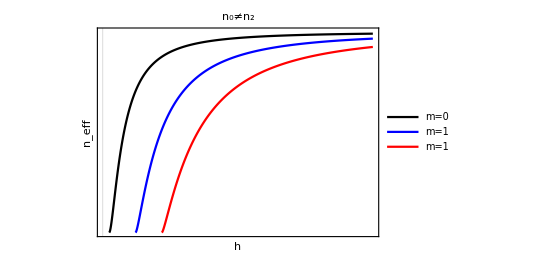

```mathematica
ListLinePlot[{result[[1]],result[[2]],result[[3]]},PlotRange->{{0,hmax},{n1,n0}},PlotTheme->"Scientific",
FrameTicks->None,FrameLabel->{"h","n_eff"},
PlotStyle->{{Black},{Blue},{Red}},AspectRatio->0.7,
PlotLegends->Placed[{"m=0","m=1","m=1"},{0.85,0.25}],
PlotLabel->"n_0≠n_2",
LabelStyle->{Black,FontFamily->"Times New Roman",20},
BaseStyle->{Black,FontFamily->"Times New Roman",20}]
```

```mathematica
k0=1;
n1=1.5;
n0=1.4;
n2=1.4;
h=.;

p0=(β^2-k0^2 n0^2)^(1/2);
p2=(β^2-k0^2 n2^2)^(1/2);
κ=(k0^2 n1^2-β^2)^(1/2);
result={};
Do[s1=m π +ArcTan[p0/κ]+ArcTan[p2/κ]-h κ;
s2=FindRoot[s1==0/.{β->n0},{h,1}];
hmin=h/.s2[[1]];
hmax=60;
s3=Table[FindRoot[s1==0,{β,1}],{h,hmin+0.01,hmax,0.1}];
L=Length[s3];
s4=Table[{(hmax-hmin)/L*(i-1)+hmin,β/.s3[[i]]},{i,1,L}];
AppendTo[result,s4],
{m,0,4}]
```

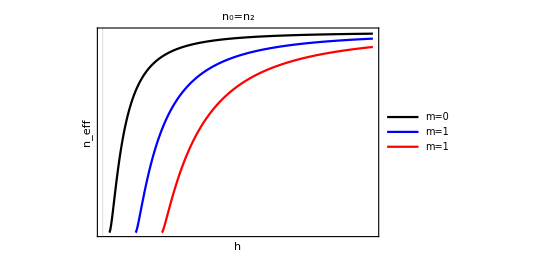

```mathematica
ListLinePlot[{result[[1]],result[[2]],result[[3]]},PlotRange->{{0,hmax},{n1,n0}},PlotTheme->"Scientific",
FrameTicks->None,FrameLabel->{"h","n_eff"},
PlotStyle->{{Black},{Blue},{Red}},AspectRatio->0.7,
PlotLabel->"n_0=n_2",
PlotLegends->Placed[{"m=0","m=1","m=1"},{0.85,0.25}],
LabelStyle->{Black,FontFamily->"Times New Roman",20}]
```

```mathematica
Clear["Global`"]
s1=Curl[{Ex[x] ⅇ^(-ⅈ(β z-ω t)),Ey[x] ⅇ^(-ⅈ(β z-ω t)),Ez[x] ⅇ^(-ⅈ(β z-ω t))},{x,y,z}]//Simplify
s1=Curl[{Hx[x] ⅇ^(-ⅈ(β z-ω t)),Hy[x] ⅇ^(-ⅈ(β z-ω t)),Hz[x] ⅇ^(-ⅈ(β z-ω t))},{x,y,z}]//Simplify
```

{ⅈ ⅇ^(ⅈ (-z β+t ω)) β Ey[x],ⅇ^(ⅈ (-z β+t ω)) (-ⅈ β Ex[x]-Ez'[x]),ⅇ^(ⅈ (-z β+t ω)) Ey'[x]}

{ⅈ ⅇ^(ⅈ (-z β+t ω)) β Hy[x],ⅇ^(ⅈ (-z β+t ω)) (-ⅈ β Hx[x]-Hz'[x]),ⅇ^(ⅈ (-z β+t ω)) Hy'[x]}

```mathematica
Solve[{B0+C0==A0,ⅈ κ1(B0-C0)==p0 A0,B0 ⅇ^(ⅈ κ1 h)+C0 ⅇ^(-ⅈ κ1 h)==D0},{B0,C0,D0}]//Simplify
```

{{B0→(A0 (-ⅈ p0+κ1))/(2 κ1),C0→(A0 (ⅈ p0+κ1))/(2 κ1),D0→(A0 ⅇ^(-ⅈ h κ1) (-ⅈ (-1+ⅇ^(2 ⅈ h κ1)) p0+(1+ⅇ^(2 ⅈ h κ1)) κ1))/(2 κ1)}}

```mathematica
Clear["Global`*"]
```

```mathematica
a=.;
R10={};
a=10;
Do[s1=m  π +ArcTan[√(b/(1-b))]+ArcTan[√((a+b)/(1-b))]-V √(1-b);
s2=FindRoot[s1==0/.{b->0},{V,m π+1}];Vmin=V/.s2[[1]];
Vmax=20;
s3=Table[FindRoot[s1==0,{b,m π}],{V,Vmin+0.01,Vmax,0.1}];
L=Length[s3];
s4=Table[{((i-1)/(L-1)*(Vmax-m π)+Vmin)/2,b/.s3[[i]]},{i,1,L}];
AppendTo[R10,s4],{m,0,6,1}]
R0={};
a=0;
Do[s1=m  π +ArcTan[√(b/(1-b))]+ArcTan[√((a+b)/(1-b))]-V √(1-b);
(*s2=FindRoot[s1==0/.{b->0},{V,m π+0.1}];*)
Vmin=m π;
Vmax=20;
s3=Table[FindRoot[s1==0,{b,2 m}],{V,Vmin+0.1,Vmax,0.11}];
L=Length[s3];
s4=Table[{((i-1)/L*(Vmax-m π)+Vmin)/2,b/.s3[[i]]},{i,1,L}];
AppendTo[R0,s4],{m,0,6,1}]
```

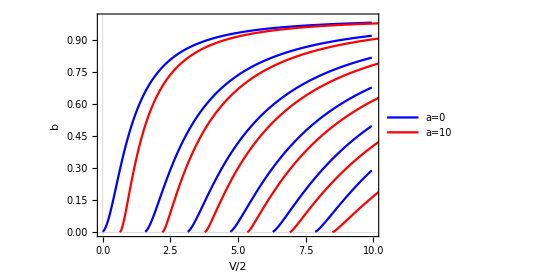

```mathematica
g10=ListLinePlot[Table[R10[[i]],{i,1,6}],PlotStyle->{{Red}},AspectRatio->0.7,PlotTheme->"Scientific",PlotLegends->Placed[{"a=10"},{0.1,0.9}],
PlotRange->{{0,10},{0,1}}];
g0=ListLinePlot[Table[R0[[i]],{i,1,6}],PlotStyle->{{Blue}},AspectRatio->0.7,PlotTheme->"Scientific",PlotLegends->Placed[{"a=0"},{0.1,0.8}],
PlotRange->{{0,10},{0,1}}];
Show[g0,g10,FrameLabel->{"V/2","b"},
LabelStyle->{Black,FontFamily->"Times New Roman",20}
]
```

```mathematica
(*TE={};
a=0;
Do[s1=m  π +ArcTan[√(b/(1-b))]+ArcTan[√((a+b)/(1-b))]-V √(1-b);
(*s2=FindRoot[s1==0/.{b->0},{V,m π+0.1}];*)
Vmin=m π;
Vmax=20;
s3=Table[FindRoot[s1==0,{b,2 m}],{V,Vmin+0.1,Vmax,0.11}];
L=Length[s3];
s4=Table[{((i-1)/L*(Vmax-m π)+Vmin)/2,b/.s3[[i]]},{i,1,L}];
AppendTo[TE,s4],{m,0,6,1}]*)
TM={};
n1=1.5;
n0=n2=1;
Do[s1=m  π +ArcTan[n1^2/n0^2 √(b/(1-b))]+ArcTan[n1^2/n2^2 √((a+b)/(1-b))]-V √(1-b);
(*s2=FindRoot[s1==0/.{b->0},{V,m π+0.1}];*)
Vmin=m π;
Vmax=20;
s3=Table[FindRoot[s1==0,{b,0.2}],{V,Vmin+0.1,Vmax,0.11}];
L=Length[s3];
s4=Table[{((i-1)/L*(Vmax-m π)+Vmin)/2,b/.s3[[i]]},{i,1,L}];
AppendTo[TM,s4],{m,0,6,1}]
```

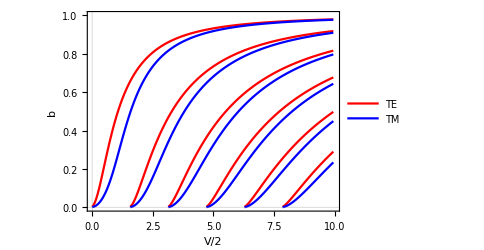

```mathematica
gTE=ListLinePlot[Table[TE[[i]],{i,1,6}],PlotStyle->{{Red}},AspectRatio->0.7,PlotTheme->"Scientific",PlotLegends->Placed[{"TE"},{0.1,0.9}],
PlotRange->{{0,10},{0,1}}];
gTM=ListLinePlot[Table[TM[[i]],{i,1,6}],PlotStyle->{{Blue}},AspectRatio->0.7,PlotTheme->"Scientific",PlotLegends->Placed[{"TM"},{0.1,0.8}],
PlotRange->{{0,10},{0,1}}];
Show[gTE,gTM,FrameLabel->{"V/2","b"},
LabelStyle->{Black,FontFamily->"Times New Roman",20}
]
```

```mathematica
Clear["Global`*"]
```

```mathematica
Lx:=D[#,{r,2}]+1/r D[#,r]+1/r^2 D[#,{ϕ,2}]+q^2#&;
s1=Lx[R[r]Φ[ϕ]] r^2//Simplify
```

r Φ[ϕ] (R'[r]+r R''[r])+R[r] (q^2 r^2 Φ[ϕ]+Φ''[ϕ])

(Φ[ϕ] (R'[r]+r R''[r]))/r+R[r] (q^2 Φ[ϕ]+Φ''[ϕ]/r^2)

```mathematica
Clear["Global`*"]
```

```mathematica
J=BesselJ[1,U]/(U BesselJ[0,U]); K=BesselK[1,W]/(W BesselK[0,W]);
W=√(V^2-U^2);
```

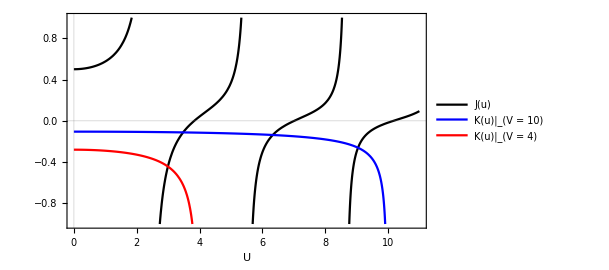

```mathematica
Plot[{J,-K/.{V->10},-K/.{V->4}},{U,0,11},PlotRange->{{0,11},{-1,1}},
PlotTheme->"Scientific",AspectRatio->0.6,FrameLabel->{"U"},PlotStyle->{{Black},{Blue},{Red}},
PlotLegends->Placed[{"J(u)","K(u)|_(V = 10)","K(u)|_(V = 4)"},{0.25,0.7}],
LabelStyle->{Black,FontFamily->"Times New Roman",16}]
```

```mathematica
m=.;
J=BesselJ[m+1,U]/(U BesselJ[m,U]); K=BesselK[m+1,W]/(W BesselK[m,W]);
m=2;
```

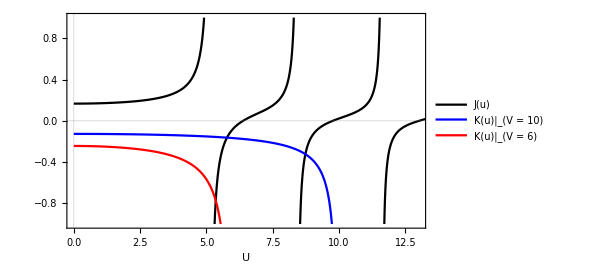

```mathematica
Plot[{J,-K/.{V->10},-K/.{V->6}},{U,0,14},PlotRange->{{0,13},{-1,1}},
PlotTheme->"Scientific",AspectRatio->0.6,FrameLabel->{"U"},PlotStyle->{{Black},{Blue},{Red}},
PlotLegends->Placed[{"J(u)","K(u)|_(V = 10)","K(u)|_(V = 6)"},{0.2,0.8}],
LabelStyle->{Black,FontFamily->"Times New Roman",16}]
```

```mathematica
m=.;
J=BesselJ[m-1,U]/(U BesselJ[m,U]); K=BesselK[m-1,W]/(W BesselK[m,W]);
m=2;
```

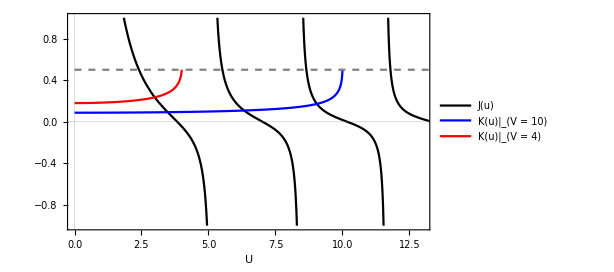

```mathematica
Plot[{J,K/.{V->10},K/.{V->4},0.5},{U,0,14},PlotRange->{{0,13},{-1,1}},
PlotTheme->"Scientific",AspectRatio->0.6,FrameLabel->{"U"},PlotStyle->{Black,Blue,Red,{Dashed,Gray}},
PlotLegends->Placed[{"J(u)","K(u)|_(V = 10)","K(u)|_(V = 4)"},{0.2,0.2}],
LabelStyle->{Black,FontFamily->"Times New Roman",16}]
```

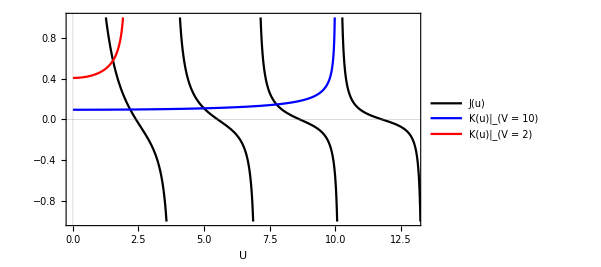

```mathematica
m=.;
J=BesselJ[m-1,U]/(U BesselJ[m,U]); K=BesselK[m-1,W]/(W BesselK[m,W]);
m=1;
Plot[{J,K/.{V->10},K/.{V->2}},{U,0,14},PlotRange->{{0,13},{-1,1}},
PlotTheme->"Scientific",AspectRatio->0.6,FrameLabel->{"U"},PlotStyle->{Black,Blue,Red},
PlotLegends->Placed[{"J(u)","K(u)|_(V = 10)","K(u)|_(V = 2)"},{0.2,0.2}],
LabelStyle->{Black,FontFamily->"Times New Roman",16}]
```